## defining model

```mathematica
changepoint=0.451985;
```

```mathematica
λ[t_]:=Piecewise[{{1,t<changepoint},{2,t≥changepoint}}]
```

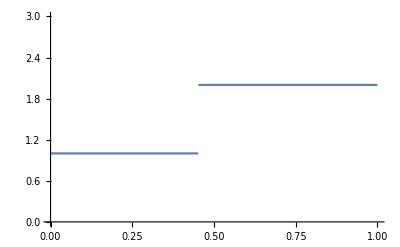

```mathematica
Plot[λ[t],{t,0,1},PlotRange->{0,3}]
```

```mathematica
ts={0,0.095310,0.200671,0.318454,changepoint,0.606136,0.788457,1.011601,1.299283,1.704748,2.397895,Infinity};
```

```mathematica
n=Length[ts]-2;
```

```mathematica
t[i_]:=ts[[i+1]];
```

```mathematica
Omega[t1_,t2_]:=Integrate[1/λ[s],{s,t1,t2}]
```

```mathematica
io[i_]:=Omega[t[i],t[i+1]]
```

```mathematica
(*Pi*)
```

## calculating probabilities and expectations

```mathematica
pi[i_,j_]:=Piecewise[{
{3/2*Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])(1-Exp[-Omega[t[j],t[j+1]]]),0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/2 Exp[-3Omega[0,t[i]]](2-3Exp[-(t[i+1]-t[i])/λ[t[i]]]+Exp[-3(t[i+1]-t[i])/λ[t[i]]]),
0≤i==j≤n&&(i∈Integers&&j∈Integers)}}]
```

```mathematica
(*Pi is working, at least for constant N [λ]*)
```

```mathematica
(*E[t_3]*)
```

```mathematica
intEt3[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t3 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et3[i_,j_]:=Piecewise[{
{3/(4pi[i,j])Exp[-3Omega[0,t[i]]](1-Exp[-Omega[t[j],t[j+1]]])Exp[-Omega[t[i+1],t[j]]]((λ[t[i]]+2t[i])Exp[-Omega[t[i],t[i+1]]]-
(λ[t[i]]+2t[i+1])Exp[-3Omega[t[i],t[i+1]]]),
0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/(12pi[i,i])Exp[-3Omega[0,t[i]]](4(3t[i]+λ[t[i]])+
Exp[-3Omega[t[i],t[i+1]]](6t[i+1]+5λ[t[i]])-9Exp[-Omega[t[i],t[i+1]]](2t[i]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[i]+λ[t[i]]/3.0,i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

```mathematica
(*Et2*)
intEt2[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t2 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et2[i_,j_]:=Piecewise[{
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]-(λ[t[j]]+t[j+1])Exp[-Omega[t[j],t[j+1]]]),
0≤i<j<n&&(i∈Integers&&j∈Integers)},
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]),
0≤i<j==n&&(i∈Integers&&j∈Integers)},
{1/(6pi[i,j])Exp[-3Omega[0,t[i]]](Exp[-3Omega[t[i],t[i+1]]](3t[i+1]+λ[t[i]])+6t[i]+8λ[t[i]]-9Exp[-Omega[t[i],t[i+1]]](t[i+1]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[n]+λ[t[n]]/3+λ[t[n]],
i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

## calculating transitions

```mathematica
intqts[i_,j_,k_,l_]:=Piecewise[{
{(*case A*)
Assuming[{s3,s2,t2,t3,u}∈Reals,Integrate[(1/(2s2+s3)Exp[-3Omega[u,s3]]Exp[-2Omega[s3,s2]]*1/λ[t2] Exp[-Omega[s2,t2]])*DiracDelta[t3-Et3[i,j]]/.{s3->Et3[i,j],s2->Et2[i,j]},{u,0,Et3[i,j]},{t2,t[l],t[l+1]},{t3,t[k],t[k+1]}]+Integrate[(2/(2s2+s3)Exp[-2Omega[u,s2]]*1/λ[t2] Exp[-Omega[s2,t2]])*DiracDelta[t3-Et3[i,j]]/.{s3->Et3[i,j],s2->Et2[i,j]},{u,Et3[i,j],Et2[i,j]},{t2,t[l],t[l+1]},{t3,t[k],t[k+1]}]]
,
0≤i==k<j<l&&{i,j,k,l}∈Integers
},
{(*case B*)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(1/(2Et2[i,j]+Et3[i,j])Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t2]]*1/λ[t2]),{u,0,Et3[i,j]},{t2,t[l],t[l+1]}]+
NIntegrate[(2/(2Et2[i,j]+Et3[i,j])1/λ[t2] Exp[-2Omega[u,t2]]),{t2,t[l],t[l+1]},{u,Et3[i,j],t2}]],
0≤i==k<l<j&&{i,j,k,l}∈Integers
},
{ (* case C *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(1/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,t3]]),{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i==l<j&&{i,j,k,l}∈Integers
},
{ (* case D *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,t3]]),{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i<j==l&&{i,j,k,l}∈Integers
},
{ (* case E *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t3]]),{t3,t[k],t[k+1]},{u,0,Et3[i,j]}]],
0≤i<k<j==l&&{i,j,k,l}∈Integers
},
{ (* case F *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],Et2[i,j]]]Exp[-Omega[Et2[i,j],t2]]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]],
0≤i<j==k<l&&{i,j,k,l}∈Integers
},
{ (* case G and G2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[1/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t2]],{t2,Et3[i,j],t[l+1]},{u,0,Et3[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-2Omega[u,t2]],{t2,Et3[i,j],t[l+1]},{u,Et3[i,j],t2}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[1/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],Et3[i,j]},{u,0,t3}]],
0≤i==k==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case H and H2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t3]],{t3,t[k],Et2[i,j]},{u,0,Et3[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],Et2[i,j]]]*Exp[-Omega[Et2[i,j],t2]],{t2,Et2[i,j],t[k+1]},{u,0,Et3[i,j]}]],
0≤i<k==l==j≤n&&{i,j,k,l}∈Integers
},
{ (* case I and I2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(Exp[-3 Omega[u,Et3[i,j]]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]]+Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2 Exp[-2 Omega[u,Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,Et3[i,j],Et2[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2 Exp[-3 Omega[u,Et3[i,j]]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]],
0≤i==j==k<l&&{i,j,k,l}∈Integers
},
{ (* case J and J2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],t[k+1]},{u,0,t3}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i==j==l&&{i,j,k,l}∈Integers
}
}]
```

```mathematica
qts[i_,j_,k_,l_]:=Piecewise[{
{(* case A *)
1/(2Et2[i,j]+Et3[i,j])1/λ[t[l]] Exp[-2Omega[Et3[i,j],Et2[i,j]]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(Exp[-2Omega[t[i+1],Et2[i,j]]](1-Exp[-2(t[i+1]-Et3[i,j])/λ[t[i]]])*λ[t[i]]/2+
Sum[Exp[-2Omega[t[a+1],Et2[i,j]]](1-Exp[-2io[a]])*λ[t[a]]/2,{a,i+1,j-1}]+(1-Exp[-2(Et2[i,j]-t[j])/λ[t[j]]])*λ[t[j]]/2)Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]]),
0<=i==k<j<l≤n&&{i,j,k,l}∈Integers
},
{ (* case B *)
1/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
Exp[-2(*notice the 2*)Omega[Et3[i,j],t[l]]]*λ[t[l]]/2(1-Exp[-2io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(1-Exp[-2(t[i+1]-Et3[i,j])/λ[t[i]]])*λ[t[i]]/2*Exp[-2Omega[t[i+1],t[l]]]*λ[t[l]]/2(1-Exp[-2io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]](λ[t[l]]/2(1-Exp[-2io[l]])Sum[(1-Exp[-2io[a]])*λ[t[a]]/2 Exp[-2Omega[t[a+1],t[l]]],{a,i+1,l-1}])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*λ[t[l]]/2(t[l+1]-t[l]-λ[t[l]]/2(1-Exp[-2io[l]])),
0<=i==k<l<j≤n&&{i,j,k,l}∈Integers
},
{(* case C *)
1/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(λ[t[k]]/3(1-Exp[-3io[k]])Sum[(1-Exp[-3io[a]])*λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]+λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case D *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(λ[t[k]]/3(1-Exp[-3io[k]])Sum[(1-Exp[-3io[a]])*λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]+λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i<j==l≤n&&{i,j,k,l}∈Integers
},
{(* case E *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*Exp[-2Omega[Et3[i,j],t[k]]]*λ[t[k]]/2(1-Exp[-2io[k]]),
0≤i<k<j==l&&{i,j,k,l}∈Integers
},
{ (* case F *)
2/(2Et2[i,j]+Et3[i,j])Exp[-2Omega[Et3[i,j],Et2[i,j]]]*1/λ[t[l]]*
(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]]*(1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]]),
0≤i<j==k<l&&{i,j,k,l}∈Integers
},
{ (* case G and G2 *)
1/(2Et2[i,j]+Et3[i,j])*(1/λ[t[k]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*λ[t[k]]/2*
(1-Exp[-2(t[k+1]-Et3[i,j])/λ[t[k]]])+t[k+1]-Et3[i,j]-λ[t[k]]/2(1-Exp[-2(t[k+1]-Et3[i,j])/λ[t[k]]]))+
1/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]](Sum[(1-Exp[-3io[a]])*λ[t[a]]/3*Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]*λ[t[k]]/3(1-Exp[-3(Et3[i,j]-t[k])/λ[t[k]]])+λ[t[k]]/3(Et3[i,j]-t[k]-λ[t[k]]/3(1-Exp[-3(Et3[i,j]-t[k])/λ[t[k]]]))),
0≤i==k==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case H and H2 *)
1/(2Et2[i,j]+Et3[i,j])*4/λ[t[k]]*Exp[-2Omega[Et3[i,j],t[k]]](Sum[Exp[-3Omega[t[a+1],Et3[i,j]]]*(1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
λ[t[k]]/2(1-Exp[-2(Et2[i,j]-t[k])/λ[t[k]]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[k]] Exp[-2Omega[Et3[i,j],Et2[i,j]]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+
(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*λ[t[k]](1-Exp[-(t[k+1]-Et2[i,j])/λ[t[k]]]),
0≤i<k==l==j&&{i,j,k,l}∈Integers
},
{ (* case I and I2 *)
1/(2 Et2[i,j]+Et3[i,j])(1/λ[t[l]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] (∑_(a=0)^(i-1) 1/3 Exp[-3 Omega[t[a+1],Et3[i,j]]] (1-Exp[-3 io[a]]) λ[t[a]]+1/3 (1-Exp[-(3 (Et3[i,j]-t[i]))/λ[t[i]]]) λ[t[i]]) Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]])+1/(λ[t[l]] 2)2 λ[t[i]] (1-Exp[-(2 (Et2[i,j]-Et3[i,j]))/λ[t[i]]]) Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]]))+
1/((2 Et2[i,j]+Et3[i,j]) λ[t[l]])2 Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]]) (∑_(a=0)^(i-1) 1/3 Exp[-3 Omega[t[a+1],Et3[i,j]]] (1-Exp[-3 io[a]]) λ[t[a]]+1/3 (1-Exp[-(3 (Et3[i,j]-t[i]))/λ[t[i]]]) λ[t[i]]),

0≤i==j==k<l&&{i,j,k,l}∈Integers
},
{ (* case J and J2 *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]](λ[t[k]]/3(1-Exp[-3io[k]])(Sum[(1-Exp[-3io[a]])λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}])+λ[t[k]]/3*
(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]])))+
2/(2Et2[i,j]+Et3[i,j])1/λ[t[k]](Sum[(1-Exp[-3io[a]])λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}] λ[t[k]]/3(1-Exp[-3io[k]])+
λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i==j==l&&{i,j,k,l}∈Integers
}
}]
```

## exporting qts

```mathematica
numStates = (n+1)(n+2)/2
```

66

```mathematica
getIndex[i_,j_,n_]:=i*n-i(i-1)/2+j+1;
```

```mathematica
allqts = Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
For[i=0,i≤n,i++,
Print[i];
For[j=i,j≤n,j++,
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
ijIdx = getIndex[i,j,n];
klIdx=getIndex[k,l,n];
allqts[[ijIdx,klIdx]]=qts[i,j,k,l];
]
]
]
]
```

0

1

2

3

4

5

6

7

8

9

10

```mathematica
Export["mathematica_qtsprobs.csv",allqts]
```

mathematica_qtsprobs.csv

```mathematica
allintqts = Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
For[i=0,i≤n,i++,
Print[i];
For[j=i,j≤n,j++,
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
ijIdx = getIndex[i,j,n];
klIdx=getIndex[k,l,n];
allintqts[[ijIdx,klIdx]]=intqts[i,j,k,l];
]
]
]
]
```

0

1

2

3

4

5

6

7

8

9

10

```mathematica
Export["mathematica_intqtsprobs.csv",allintqts]
```

mathematica_intqtsprobs.csv

```mathematica
pts[i_,j_,k_,l_,ρ_]:=
```

## making pts transitions

```mathematica
pts[i_,j_,k_,l_,ρ_]:=Module[{treeSize, probRecomb},treeSize=3*Et3[i,j]+2*(Et2[i,j]-Et3[i,j]); probRecomb=1-Exp[-treeSize*ρ/2];qts[i,j,k,l]*probRecomb]
```

## defining emission probabilities

```mathematica
emit[k_,i_,j_,Td_,θ_]:=Piecewise[{
{
Exp[(-θ(2Et2[i,j]+Et3[i,j]+3Td))/2],
k==0
},
{
Exp[-θ/2*(Et2[i,j]-Et3[i,j])](1-Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)]),
k==1
},
{
(1-Exp[-θ/2(Et2[i,j]-Et3[i,j])])Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)],
k==2
},
{
(1-Exp[-θ/2(Et2[i,j]-Et3[i,j])])(1-Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)]),
k==3
}
}]
```

## emissions exporting

```mathematica
numStates = (n+1)(n+2)/2;
```

```mathematica
ρ=0.001;θ=0.001;Td=0.2;
```

```mathematica
emissionsout =Table[0,{i,1,numStates},{j,1,6}];
```

```mathematica
getIndex[i_,j_,n_]:=i*n-i(i-1)/2+j+1;
```

```mathematica
Module[{state,i,j,k},
For[i=0,i≤n,i++,
For[j = i, j≤n,j++,
state=getIndex[i,j,n];
emissionsout[[state,1]] = i;
emissionsout[[state,2]] = j;
For[k=0,k≤3,k++,
emissionsout[[state,k+3]] = emit[k,i,j,Td,θ];
Print[emissionsout[[state,k+3]]]
]
]
]
]
```

```mathematica
emissionsout//TableForm
```

0 | 0 | 0.999622 | 0.000361719 | 0.0000159948 | 5.78781×10^-9
0 | 1 | 0.99953 | 0.000419565 | 0.0000504394 | 2.11726×10^-8
0 | 2 | 0.999419 | 0.000475182 | 0.000106076 | 5.04349×10^-8
0 | 3 | 0.999293 | 0.000537773 | 0.000168691 | 9.07817×10^-8
0 | 4 | 0.999149 | 0.000609844 | 0.000240788 | 1.46968×10^-7
0 | 5 | 0.998982 | 0.000693632 | 0.000324607 | 2.25387×10^-7
0 | 6 | 0.99878 | 0.000794465 | 0.000425477 | 3.3844×10^-7
0 | 7 | 0.998526 | 0.000921205 | 0.000552264 | 5.09499×10^-7
0 | 8 | 0.998183 | 0.00109234 | 0.00072346 | 7.91701×10^-7
0 | 9 | 0.997648 | 0.00135954 | 0.000990758 | 1.35015×10^-6
0 | 10 | 0.99529 | 0.00253633 | 0.00216799 | 5.52475×10^-6
1 | 1 | 0.999471 | 0.00051093 | 0.000017691 | 9.04365×10^-9
1 | 2 | 0.999369 | 0.000575147 | 0.0000560986 | 3.22854×10^-8
1 | 3 | 0.999243 | 0.000637729 | 0.000118713 | 7.57643×10^-8
1 | 4 | 0.999099 | 0.000709789 | 0.000190811 | 1.35557×10^-7
1 | 5 | 0.998932 | 0.000793564 | 0.000274629 | 2.18169×10^-7
1 | 6 | 0.99873 | 0.000894382 | 0.0003755 | 3.36267×10^-7
1 | 7 | 0.998476 | 0.0010211 | 0.000502286 | 5.13669×10^-7
1 | 8 | 0.998134 | 0.00119221 | 0.000673482 | 8.04434×10^-7
1 | 9 | 0.997598 | 0.00145937 | 0.00094078 | 1.37625×10^-6
1 | 10 | 0.99524 | 0.00263598 | 0.00211801 | 5.60974×10^-6
2 | 2 | 0.999304 | 0.00067662 | 0.0000197898 | 1.33995×10^-8
2 | 3 | 0.999188 | 0.000748792 | 0.0000631914 | 4.73557×10^-8
2 | 4 | 0.999044 | 0.000820839 | 0.000135289 | 1.11157×10^-7
2 | 5 | 0.998876 | 0.0009046 | 0.000219107 | 1.98427×10^-7
2 | 6 | 0.998674 | 0.0010054 | 0.000319978 | 3.22133×10^-7
2 | 7 | 0.998421 | 0.0011321 | 0.000446765 | 5.06583×10^-7
2 | 8 | 0.998078 | 0.00130318 | 0.00061796 | 8.06864×10^-7
2 | 9 | 0.997543 | 0.00157029 | 0.000885258 | 1.39354×10^-6
2 | 10 | 0.995185 | 0.00274671 | 0.00206249 | 5.69247×10^-6
3 | 3 | 0.999115 | 0.000862889 | 0.0000224544 | 1.93928×10^-8
3 | 4 | 0.998981 | 0.00094577 | 0.000072838 | 6.89582×10^-8
3 | 5 | 0.998814 | 0.00102952 | 0.000156656 | 1.61472×10^-7
3 | 6 | 0.998612 | 0.0011303 | 0.000257527 | 2.91487×10^-7
3 | 7 | 0.998358 | 0.00125697 | 0.000384314 | 4.83867×10^-7
3 | 8 | 0.998016 | 0.00142802 | 0.00055551 | 7.94856×10^-7
3 | 9 | 0.997481 | 0.00169508 | 0.000822808 | 1.39825×10^-6
3 | 10 | 0.995123 | 0.00287128 | 0.00200004 | 5.77081×10^-6
4 | 4 | 0.998896 | 0.00107784 | 0.0000258176 | 2.78581×10^-8
4 | 5 | 0.998741 | 0.00117425 | 0.0000843126 | 9.91286×10^-8
4 | 6 | 0.99854 | 0.00127501 | 0.000185183 | 2.36455×10^-7
4 | 7 | 0.998286 | 0.00140166 | 0.00031197 | 4.38026×10^-7
4 | 8 | 0.997943 | 0.00157267 | 0.000483166 | 7.61424×10^-7
4 | 9 | 0.997408 | 0.00183967 | 0.000750464 | 1.38419×10^-6
4 | 10 | 0.995051 | 0.00301561 | 0.00192769 | 5.84209×10^-6
5 | 5 | 0.998643 | 0.00132663 | 0.0000305583 | 4.05946×10^-8
5 | 6 | 0.998456 | 0.00144232 | 0.000101561 | 1.4671×10^-7
5 | 7 | 0.998202 | 0.00156893 | 0.000228348 | 3.58909×10^-7
5 | 8 | 0.99786 | 0.0017399 | 0.000399544 | 6.96658×10^-7
5 | 9 | 0.997325 | 0.00200684 | 0.000666842 | 1.34183×10^-6
5 | 10 | 0.994968 | 0.00318248 | 0.00184407 | 5.89841×10^-6
6 | 6 | 0.998337 | 0.00162528 | 0.0000374412 | 6.09537×10^-8
6 | 7 | 0.998102 | 0.00177008 | 0.000127821 | 2.26684×10^-7
6 | 8 | 0.997759 | 0.001941 | 0.000299017 | 5.81695×10^-7
6 | 9 | 0.997225 | 0.00220786 | 0.000566315 | 1.25382×10^-6
6 | 10 | 0.994867 | 0.00338315 | 0.00174354 | 5.9291×10^-6
7 | 7 | 0.997952 | 0.00199916 | 0.0000483517 | 9.68612×10^-8
7 | 8 | 0.997633 | 0.00219335 | 0.000172913 | 3.80157×10^-7
7 | 9 | 0.997099 | 0.00246011 | 0.00044021 | 1.08612×10^-6
7 | 10 | 0.994742 | 0.00363495 | 0.00161744 | 5.91039×10^-6
8 | 8 | 0.997431 | 0.00250028 | 0.0000683438 | 1.71319×10^-7
8 | 9 | 0.996929 | 0.00279934 | 0.000270698 | 7.60109×10^-7
8 | 10 | 0.994573 | 0.00397358 | 0.00144793 | 5.78485×10^-6
9 | 9 | 0.996614 | 0.0032685 | 0.000117462 | 3.85228×10^-7
9 | 10 | 0.994313 | 0.00449502 | 0.00118707 | 5.36643×10^-6
10 | 10 | 0.993127 | 0.00587361 | 0.000993624 | 5.87655×10^-6

```mathematica
Export["/home/peter/bio/snail/tsmc/emissions_mma_output.csv",emissionsout];
```

## α’s and β’s, γ, ξ check (forward and backward, expected transitions and conditional probs)

```mathematica
data = {0,0,1,0};
```

```mathematica
alpha = Table[0,{i,1,4},{j,1,numStates}];
```

```mathematica
beta = Table[0,{i,1,4},{j,1,numStates}];
```

```mathematica
normconst=Table[0,{i,1,4}];
```

```mathematica
(* first alphas *)
```

```mathematica
idxij=Flatten[Table[{i,j,getIndex[i,j,n]},{i,0,n},{j,i,n}],1];
```

```mathematica
pisijidx=Table[Module[{i,j},i=getI[x];j=getJ[x];pi[i,j]],{x,1,numStates}];
```

```mathematica
emitsijidx=Table[Module[{i,j,t},i=getI[x];j=getJ[x];emit[data[[l]],i,j,Td,θ]],{x,1,numStates},{l,1,4}];
```

```mathematica
(*ptsijidx=Table[
Module[{i,j,k,l},
i=getI[x];j=getJ[x];k=getI[y];l=getJ[y];pts[i,j,k,l,ρ]],
{x,1,numStates},{y,1,numStates}];
For[i=1,i≤numStates,i++,
ptsijidx[[i,i]]=1-Total[ptsijidx[[i,All]]];
Export["/home/peter/bio/snail/tsmc/ptsijidx_lambdas1.csv",ptsijidx];
]*)
```

```mathematica
ptsijidx=Import["/home/peter/bio/snail/tsmc/ptsijidx_lambdas1.csv"];
```

```mathematica
getI[ijidx_]:=idxij[[ijidx,1]]
```

```mathematica
getJ[ijidx_]:=idxij[[ijidx,2]]
```

```mathematica
alpha1 = Table[pisijidx[[x]]*emitsijidx[[x,1]] ,{x,1,numStates}];
```

```mathematica
normconst[[1]]=Total[alpha1];
```

```mathematica
alpha1 = alpha1/Total[alpha1];
```

```mathematica
alpha[[1,All]]=alpha1;
```

```mathematica
Module[{ijidx,s},
For[s=1,s≤3,s++,
For[ijidx=1,ijidx≤numStates,ijidx++,
alpha[[s+1,ijidx]]=Total[ptsijidx[[All,ijidx]]*alpha[[s,All]]]*emitsijidx[[ijidx,s+1]];
];
normconst[[s+1]]=Total[alpha[[s+1,All]]];
alpha[[s+1,All]]=alpha[[s+1,All]]/normconst[[s+1]];
];
]
```

```mathematica
Export["/home/peter/bio/snail/tsmc/forward_mma.csv",alpha];
```

```mathematica
beta4=Table[1,{ijidx,1,numStates}];
```

```mathematica
beta[[4,All]]=beta4;
```

```mathematica
Module[{ijidx,s},
For[s=3,s≥1,s--,
For[ijidx=1,ijidx≤numStates,ijidx++,
beta[[s,ijidx]]=Total[beta[[s+1,All]]*ptsijidx[[ijidx,All]]*emitsijidx[[All,s+1]]];
];
beta[[s,All]]=beta[[s,All]]/normconst[[s+1]];
]
]
```

```mathematica
(*
Export["/home/peter/bio/snail/tsmc/backward_mma.csv",beta];
*)
```

```mathematica
beta=Import["/home/peter/bio/snail/tsmc/backward_mma.csv"];
```

```mathematica
normconst (* this matches, as it has to if alpha and beta are correct... *)
```

{0.997251,0.997254,0.00183299,0.99617}

```mathematica
gamma=Table[alpha[[s,ijidx]]*beta[[s,ijidx]]/Total[alpha[[s,All]]*beta[[s,All]]],{s,1,4},{ijidx,1,numStates}];
```

```mathematica
(* Export["/home/peter/bio/snail/tsmc/gamma_mma.csv",gamma];*)
gamma = Import["/home/peter/bio/snail/tsmc/gamma_mma.csv"];
```

```mathematica
xi=Table[gamma[[s,ijidx]]*ptsijidx[[ijidx,klidx]]*emitsijidx[[klidx,s+1]]beta[[s+1,klidx]]/(normconst[[s+1]]*beta[[s,ijidx]]),{s,1,3},{ijidx,1,numStates},{klidx,1,numStates}];
```

```mathematica
Length[xi[[1]]]
```

66

```mathematica
Export["/home/peter/bio/snail/tsmc/expect_mma.csv",Total[xi,{1}]];
```

## loglike test

```mathematica
loglike=Total[gamma[[1,All]]*Log[pisijidx[[All]]]]+
Total[Flatten[Table[Log[emitsijidx[[j,s]]]gamma[[s,j]],{s,1,4},{j,1,numStates}]]]+
Total[Flatten[Table[If[ptsijidx[[i,j]]>0,Log[ptsijidx[[i,j]]],0]xi[[s,i,j]],{i,1,numStates},{j,1,numStates},{s,1,3}]]]
```

-9.9617

```mathematica
(* matches... *)
```